35

45

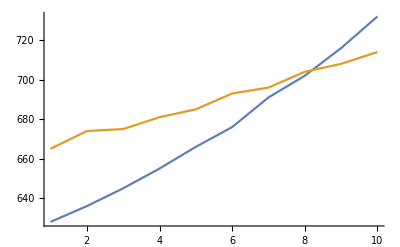

```mathematica
min=35
max=45
ListPlot[{(-Differences@datlM[[min;;max]]),(-Differences@datlF[[min;;max]])},PlotRange->All,Joined->True]
```

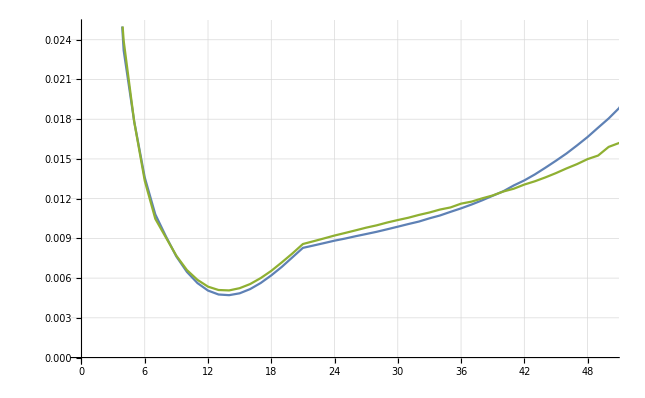

```mathematica
ListPlot[
{(-Differences@datlM)/datlM[[;;-2]],{-1},
(-Differences@datlF)/datlF[[;;-2]]}
,PlotRange->{{0,50},{0,.025}},Joined->True,GridLines->Automatic]
```

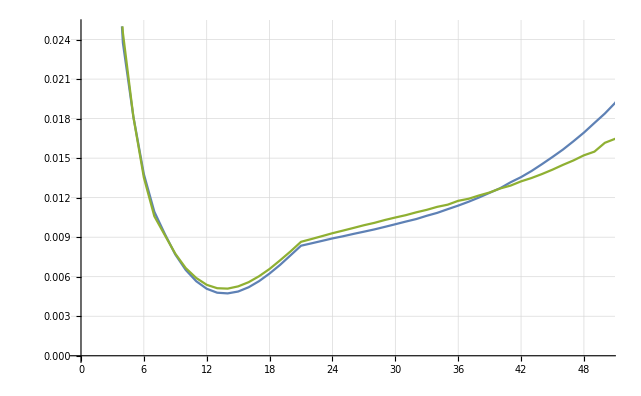

```mathematica
ListPlot[
{(-Differences@datlM)/datlM[[2;;]],{-1},
(-Differences@datlF)/datlF[[2;;]]}
,PlotRange->{{0,50},{0,.025}},Joined->True,GridLines->Automatic]
```

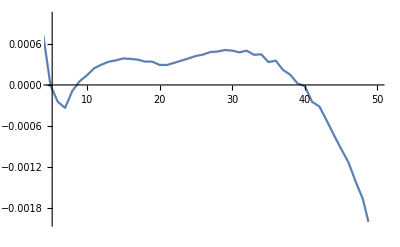

```mathematica
ListPlot[
(-Differences@datlF)/datlF[[;;-2]]-
(-Differences@datlM)/datlM[[;;-2]]
,PlotRange->{{5,50},{-.002,.001}},Joined->True]
```